# Comparação entre o comportamento da Linha Media e Linha Longa

## Antonio C S Lima Abril 2024

## Inicio

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Library/CloudStorage/Dropbox/[07] Codes/[EEE457]_codes

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,
Axes-> False,Frame-> True,PlotRange->All];
```

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Circuito de 138 kV

a partir dos dados do circuito 138CST1 do relatório da EPE, com o condutor DOVE

```mathematica
z1= 0.1160 + I.4821;
y1=I 3.4379  10^-6;
γ = Sqrt[z1 y1];
Zc= Sqrt[z1/y1];
a[x_]:=Cosh[γ x]
b[x_]:= Zc Sinh[γ x]
c[x_]:= 1/Zc Sinh[γ x]
```

### comparando os elementos do quadripolo

Comparando os elementos para distância próxima da validade da linha média (250 km)

Erros percentuais

```mathematica
TableForm[{{"A (250km)" ,"B (250km)" ,"C (250km)"  },{100 Abs[(1 +z1 x y1 x/2-a[x])/a[x]], 100 Abs[(z1 x -b[x])/b[x]],100 Abs[(y1 x (1 + z1 x y1 x/4)-c[x])/c[x]]}}/.x->250]
```

A (250km) | B (250km) | C (250km)
0.0496846 | 1.79744 | 0.912724

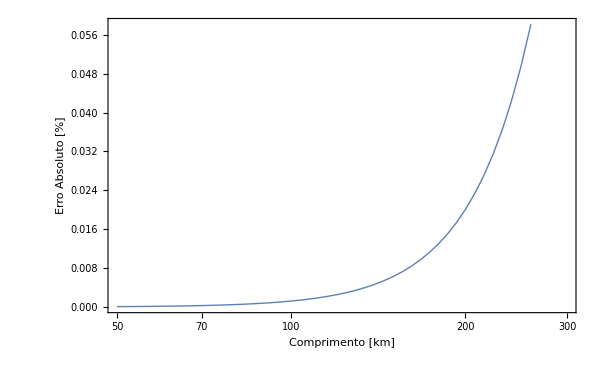

```mathematica
LogLinearPlot[100 Abs[(1 +z1 x y1 x/2-a[x])/a[x]],{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```

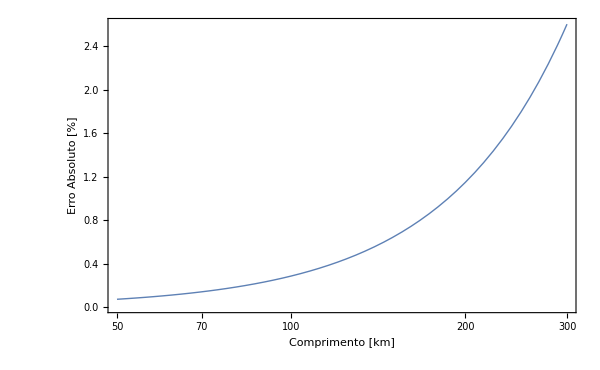

```mathematica
LogLinearPlot[{ 100 Abs[(z1 x -b[x])/b[x]]},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```

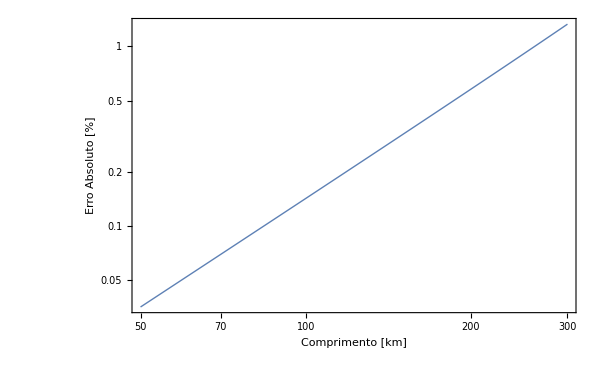

```mathematica
LogLogPlot[{100 Abs[(y1 x (1 + z1 x y1 x/4)-c[x])/c[x]]},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```

## Circuito de 230 kV

a partir dos dados do circuito 138CSH1 do relatório da EPE, com o condutor GROSSBEAK

```mathematica
z1= 0.1020 + I.5094;
y1=I 3.2599  10^-6;
γ = Sqrt[z1 y1];
Zc= Sqrt[z1/y1];
a[x_]:=Cosh[γ x]
b[x_]:= Zc Sinh[γ x]
c[x_]:= 1/Zc Sinh[γ x]
```

### comparando os elementos do quadripolo

```mathematica
TableForm[{{"A (250km)" ,"B (250km)" ,"C (250km)"  },{100 Abs[(1 +z1 x y1 x/2-a[x])/a[x]], 100 Abs[(z1 x -b[x])/b[x]],100 Abs[(y1 x (1 + z1 x y1 x/4)-c[x])/c[x]]}}/.x->250]
```

A (250km) | B (250km) | C (250km)
0.0490418 | 1.78571 | 0.906798

comportamento para comprimentos até 300 km

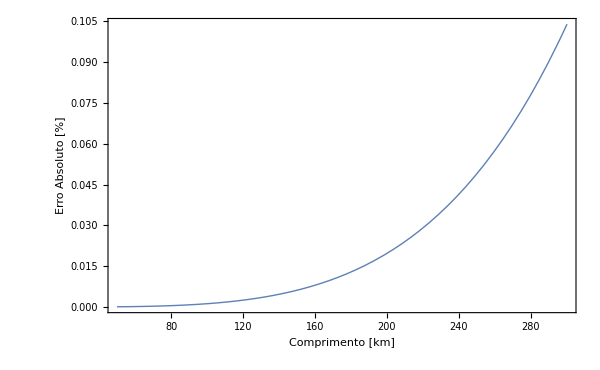

```mathematica
Plot[100 Abs[(1 +z1 x y1 x/2-a[x])/a[x]],{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```

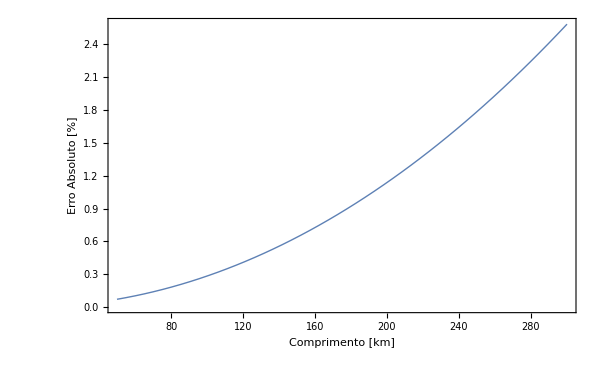

```mathematica
Plot[{ 100 Abs[(z1 x -b[x])/b[x]]},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```

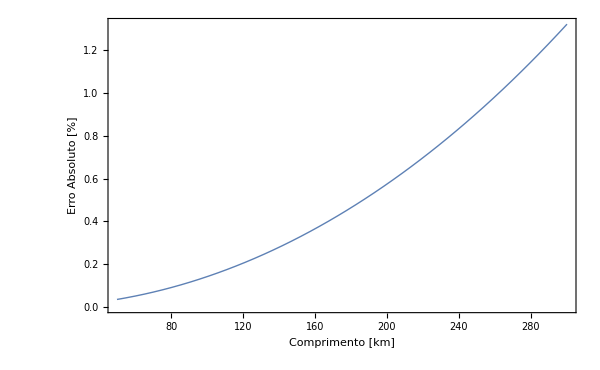

```mathematica
Plot[{100 Abs[(y1 x (1 + z1 x y1 x/4)-c[x])/c[x]]},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Erro Absoluto [%]"}]
```